# Projektna naloga

Opis: S funkcijami izrišemo logo in nato delamo različne transformacije z njim. Možne so tranformacije ki se tičejo funkcij, kar so premiki in raztegi.
Risanje logota: vsaka funkcija predstavla neko krivuljo. Moramo samo najditi pravo krivuljo in če potrebno jo omejiti. Za našo nalogo bomo izrisali logo batman-a.

# Risanje logota

(predogled)

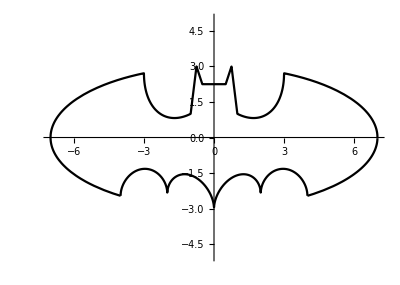

```mathematica
Show[bat1,bat2,bat3]
```

1. Za robove kril moramo pravilno omejiti elipso z enačbo (x/7)^2 + (y/3)^2 - 1 = 0, ki zgleda takole:

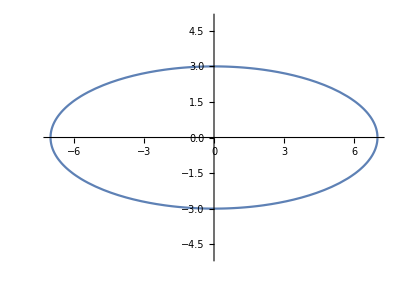

```mathematica
Plot[y /. Solve[(x/7)^2 + (y/3)^2 - 1 == 0], {x,-8,8},PlotRange->{-5,5},AspectRatio->Automatic]
```

Seddaj to elipso če omejimo.

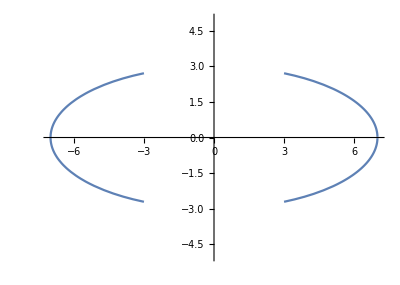

```mathematica
Plot[y /. Solve[(x/7)^2 + (y/3)^2 - 1 == 0], {x,-10,10},PlotRange->{-5,5},AspectRatio->Automatic, RegionFunction->Function[{x},Abs[x]>3]]
```

Razdelimo na dele.
Spodnja krila:

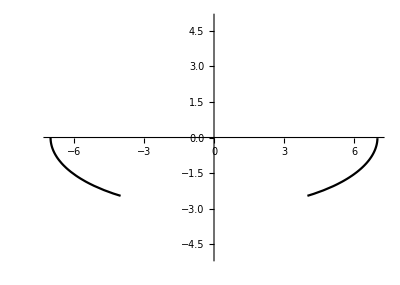

```mathematica
f1 = -3*√(1-(x/7)^2);
bat1 = Plot[f1, {x,-10,10},PlotRange->{-5,5},AspectRatio->Automatic, RegionFunction->Function[{x},Abs[x]>4],PlotStyle->Black]
```

Enačba za zgornja krila (rabimo za pozneje):

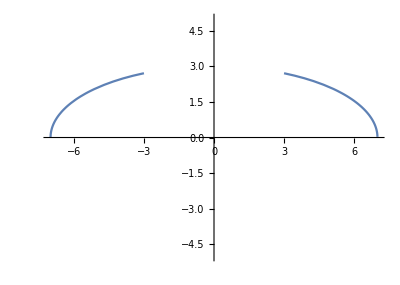

```mathematica
Krivulja1 = Plot[3*√(1-(x/7)^2), {x,-10,10},PlotRange->{-5,5},AspectRatio->Automatic, RegionFunction->Function[{x},Abs[x]>3]]
```

2. Spodnji del kril dobimo če seštejemo naslednje dve funkciji:
y =|x/2|−(3 √33−7)/112 x^2−3 in

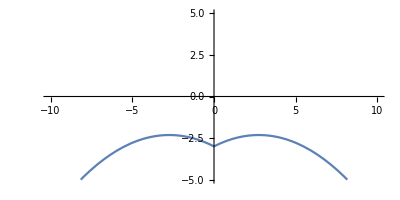

```mathematica
Plot[y /. Solve[y ==Abs[x/2]−(3 √33−7)/112 x^2−3], {x,-10,10},PlotRange->{-5,5},AspectRatio->Automatic]
```

y=√(1−(||x|−2|−1)^2)

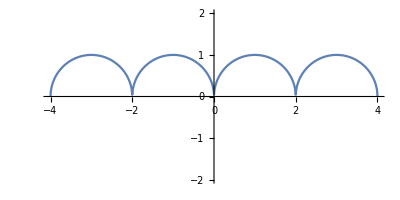

```mathematica
Plot[y /. Solve[y==√(1−(Abs[Abs[x]−2]−1)^2)], {x,-10,10},PlotRange->{-2,2},AspectRatio->Automatic]
```

Seštevek y =|x/2|−(3 √33−7)/112 x^2−3+√(1−(||x|−2|−1)^2)

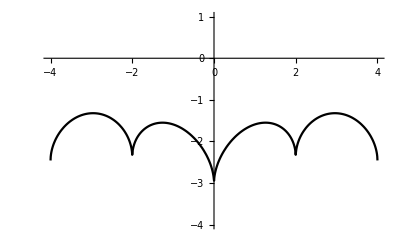

```mathematica
f2 = Abs[x/2]−(3 √33−7)/112 x^2−3+√(1−(Abs[Abs[x]−2]−1)^2);
bat2 =Plot[f2, {x,-10,10},PlotRange->{-4,1},AspectRatio->Automatic,PlotStyle->Black]
```

3. Naslednje tri krivulje so preproste črte, ki tvorijo glavo.
y =   9 - 8 |x|, omejena na 0.75 < |x| < 1

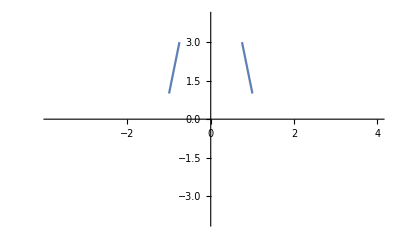

```mathematica
Krivulja2 =Plot[y /. Solve[y==9-8Abs[x]], {x,-4,4},PlotRange->{-4,4},RegionFunction->Function[{x},0.75<Abs[x]<1]]
```

y = 3 |x| + 0.75, omejena na 0.5 < |x| < 0.75

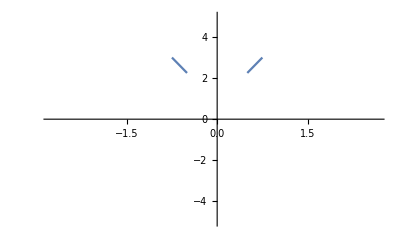

```mathematica
Krivulja3 =Plot[y /. Solve[y==3Abs[x]+0.75],{x,-5,5},PlotRange->{-5,5},RegionFunction->Function[{x},0.5<Abs[x]<0.75]]
```

y = 2.25 omejena na −0.5 < x < 0.5

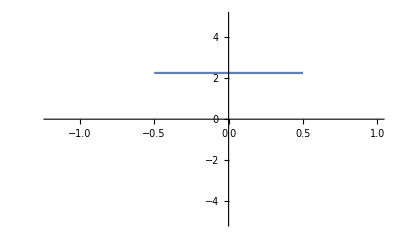

```mathematica
Krivulja4 =Plot[y /. Solve[y==2.25],{x,-5,5},PlotRange->{-5,5},RegionFunction->Function[{x},−0.5<x<0.5]]
```

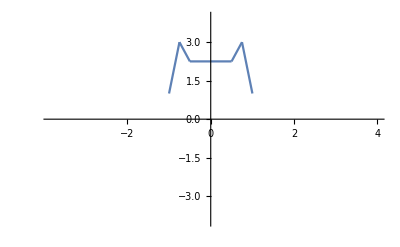

```mathematica
Show[Krivulja2,Krivulja3,Krivulja4]
```

4. Začetek kril je krivulja
 y =(6 √10)/7+(1.5−0.5Abs[x])-((6 √10)/14)√(4-(Abs[x]-1)^2) ki jo omejimo na |x| > 1

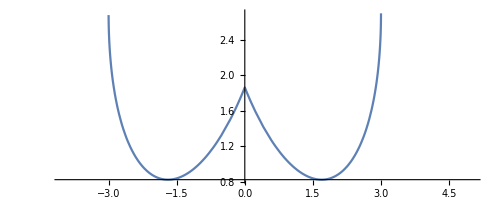

```mathematica
Plot[y /. Solve[y ==(6 √10)/7+(1.5−0.5Abs[x])-((6 √10)/14)√(4-(Abs[x]-1)^2)], {x,-4,5},AspectRatio-> Automatic]
```

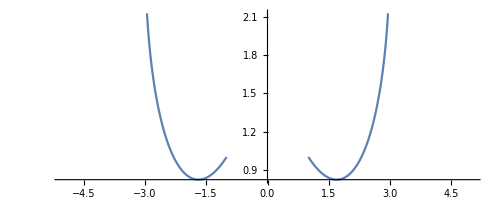

```mathematica
Krivulja5 =Plot[y /. Solve[y ==(6 √10)/7+((3−Abs[x])/2)-((3 √10)/7)√(4-(Abs[x]-1)^2)], {x,-5,5},AspectRatio->Automatic,RegionFunction->Function[{x},Abs[x]>1]]
```

Če damo sedaj vse krivluje skupaj, vidimo da so nekje luknje.

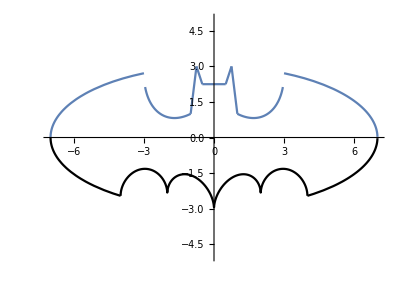

```mathematica
Show[bat1,bat2,Krivulja1,Krivulja2,Krivulja3,Krivulja4,Krivulja5]
```

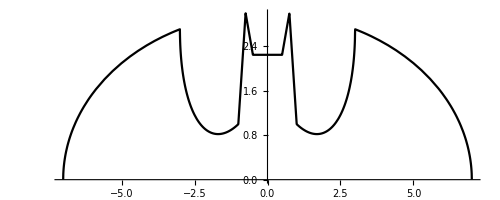

```mathematica
bat3 =Plot[{With[{krila=3*√(1-(x/7)^2),
l=(6 √10)/7+((3+x)/2)-((3 √10)/7)√(4-(Abs[x]-1)^2),
h=(3 (Abs[x-1/2]+Abs[x+1/2]+6)-11 (Abs[x-3/4]+Abs[x+3/4]))/2,

r=(6 √10)/7+((3−x)/2)-((3 √10)/7)√(4-(Abs[x]-1)^2)},krila+(l-krila) UnitStep[x+3]+(h-l) UnitStep[x+1]+(r-h) UnitStep[x-1]+(krila-r) UnitStep[x-3]]},{x,-7,7},AspectRatio->Automatic,PlotStyle->Black]
```

```mathematica
Show[bat1,bat2,bat3]
```

-Graphics-

# Transformacije

Premik po y osi.

```mathematica
Manipulate[Plot[{With[{w=3 Sqrt[1-(x/7)^2]+i,
l=6/7 Sqrt[10]+(3+x)/2-3/7 Sqrt[10] Sqrt[4-(x+1)^2]+i,
h=(3 (Abs[x-1/2]+Abs[x+1/2]+6)-11 (Abs[x-3/4]+Abs[x+3/4]))/2+i,
r=6/7 Sqrt[10]+(3-x)/2-3/7 Sqrt[10] Sqrt[4-(x-1)^2]+i},
w+(l-w) UnitStep[x+3]+(h-l) UnitStep[x+1]+(r-h) UnitStep[x-1]+(w-r) UnitStep[x-3]],1/2 (3 Sqrt[1-(x/7)^2]+Sqrt[1-(Abs[Abs[x]-2]-1)^2]+Abs[x/2]-((3 Sqrt[33]-7)/112) x^2-3) (Sign[x+4]-Sign[x-4])-3*Sqrt[1-(x/7)^2]+i},{x,-7,7},AspectRatio->Automatic,PlotRange->{-15,15},PlotStyle->Black],{i,-10,10}]
```

Premik po x osi (z avtizmom).

```mathematica
Manipulate[Plot[{With[{w=3 Sqrt[1-((x+i)/7)^2],
l=6/7 Sqrt[10]+(3+(x+i))/2-3/7 Sqrt[10] Sqrt[4-((x+i)+1)^2],
h=(3 (Abs[(x+i)-1/2]+Abs[(x+i)+1/2]+6)-11 (Abs[(x+i)-3/4]+Abs[(x+i)+3/4]))/2,
r=6/7 Sqrt[10]+(3-(x+i))/2-3/7 Sqrt[10] Sqrt[4-((x+i)-1)^2]},
w+(l-w) UnitStep[(x+i)+3]+(h-l) UnitStep[(x+i)+1]+(r-h) UnitStep[(x+i)-1]+(w-r) UnitStep[(x+i)-3]],1/2 (3 Sqrt[1-((x+i)/7)^2]+Sqrt[1-(Abs[Abs[(x+i)]-2]-1)^2]+Abs[(x+i)/2]-((3 Sqrt[33]-7)/112) (x+i)^2-3) (Sign[(x+i)+4]-Sign[(x+i)-4])-3*Sqrt[1-((x+i)/7)^2]},{x,-20,20},AspectRatio->Automatic,PlotRange->{-5,5},PlotStyle->Black],{i,-10,10}]
```

Razteg po y osi.

```mathematica
Manipulate[Plot[{With[{w=(3 Sqrt[1-(x/7)^2])*i,
l=(6/7 Sqrt[10]+(3+x)/2-3/7 Sqrt[10] Sqrt[4-(x+1)^2])*i,
h=((3 (Abs[x-1/2]+Abs[x+1/2]+6)-11 (Abs[x-3/4]+Abs[x+3/4]))/2)*i,
r=(6/7 Sqrt[10]+(3-x)/2-3/7 Sqrt[10] Sqrt[4-(x-1)^2])*i},
w+(l-w) UnitStep[x+3]+(h-l) UnitStep[x+1]+(r-h) UnitStep[x-1]+(w-r) UnitStep[x-3]],(1/2 (3 Sqrt[1-(x/7)^2]+Sqrt[1-(Abs[Abs[x]-2]-1)^2]+Abs[x/2]-((3 Sqrt[33]-7)/112) x^2-3) (Sign[x+4]-Sign[x-4])-3*Sqrt[1-(x/7)^2])*i},{x,-7,7},AspectRatio->Automatic,PlotRange->{-20,20},PlotStyle->Black],{i,-6,6}]
```

Razteg po x osi (s še več avtizmom).

```mathematica
Manipulate[Plot[{With[{w=3 Sqrt[1-((x*i)/7)^2],
l=6/7 Sqrt[10]+(3+(x*i))/2-3/7 Sqrt[10] Sqrt[4-((x*i)+1)^2],
h=(3 (Abs[(x*i)-1/2]+Abs[(x*i)+1/2]+6)-11 (Abs[(x*i)-3/4]+Abs[(x*i)+3/4]))/2,
r=6/7 Sqrt[10]+(3-(x*i))/2-3/7 Sqrt[10] Sqrt[4-((x*i)-1)^2]},
w+(l-w) UnitStep[(x*i)+3]+(h-l) UnitStep[(x*i)+1]+(r-h) UnitStep[(x*i)-1]+(w-r) UnitStep[(x*i)-3]],1/2 (3 Sqrt[1-((x*i)/7)^2]+Sqrt[1-(Abs[Abs[(x*i)]-2]-1)^2]+Abs[(x*i)/2]-((3 Sqrt[33]-7)/112) (x*i)^2-3) (Sign[(x*i)+4]-Sign[(x*i)-4])-3*Sqrt[1-((x*i)/7)^2]},{x,-20,20},AspectRatio->Automatic,PlotRange->{{-20,20},{-5,5}},PlotStyle->Black],{i,-5,5}]
```